# Two Field Potential

Bounce

BounceFunction[<|Action -> 4952.69, Bounce -> <<1>>, <<11>>, Radii -> {0.506018, 0.634889, 0.670938, 0.693035, 0.709317, 0.722422, 0.733542, 0.74332, 0.752147, 0.760275, 0.767884, 0.775103, 0.782033, 0.788757, 0.795341, 0.801845, 0.808325, 0.814834, 0.821424, 0.828152, 0.835086, 0.842317, 0.849961, 0.858173, 0.867173, 0.877292, 0.889075, 0.903523, 0.922815, 0.953404, 1.04744}|>]

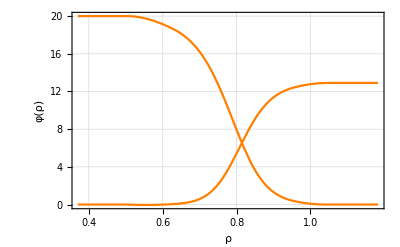

```mathematica
SetDirectory[FileNameTake[NotebookDirectory[],{1,-4}]];
<<FindBounce.m
Module[{μ2={80,100},λ={.1,.3},α = 2,ϵ = {0,0},ϕs,ϕ1,ϕ2,Extrema0},
V[ϕ_]:=Sum[-μ2[[i]] (ϕ[[i]])^2 +λ[[i]](ϕ[[i]])^4+ϵ[[i]]ϕ[[i]] ,{i,1,2}]+ α(ϕ[[1]])^2 (ϕ[[2]])^2;
dV[ϕ_]:= {2 α ϕ⟦1⟧ ϕ⟦2⟧^2-2 ϕ⟦1⟧ μ2⟦1⟧+4 ϕ⟦1⟧^3 λ⟦1⟧+ϵ⟦1⟧,2 α ϕ⟦1⟧^2 ϕ⟦2⟧-2 ϕ⟦2⟧ μ2⟦2⟧+4 ϕ⟦2⟧^3 λ⟦2⟧+ϵ⟦2⟧};
Extrema0 = {{0,12.9099},{6.25901,6.00687},{20.,0.}};
ϕs ={ϕ1,ϕ2};
Extrema = Table[ϕs/.Chop@FindRoot[dV[ϕs],Transpose@{ϕs,Extrema0[[i]]}],{i,3}];
];
PB2 = FindBounce[V[{φ1,φ2}],{φ1,φ2},Extrema[[{1,3}]],"InitialFieldValue"->Extrema[[2]], "Segments"->30]
BouncePlot[PB2]
```

Path

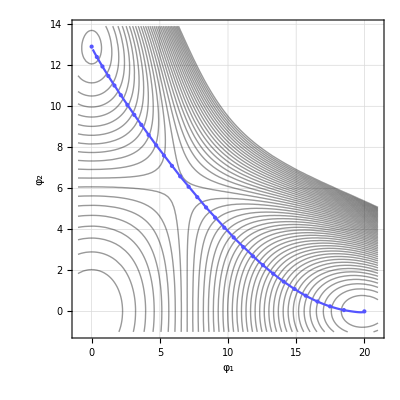

```mathematica
bounce=PB2["Bounce"];
R=Last@PB2["BounceParameters"];
markers=bounce/@R;
pBounce2 =Show[ParametricPlot[bounce[ρ],{ρ,0,1},PlotStyle->Lighter@Blue]];
contourV = ContourPlot[ V[{ϕ1,ϕ2}],{ϕ1,-1,21},{ϕ2,-1,Extrema[[1,2]]+1},PlotRange->{Automatic,5000},ContourShading->None,GridLines->Automatic,Contours->50,GridLinesStyle->Directive[Dashed,GrayLevel[.85]],ContourStyle->Opacity[0.4],FrameLabel->{"φ_1","φ_2"},ImageSize->400,LabelStyle->Directive[Black,FontSize->25, FontFamily->"Times New Roman",FontSlant->Plain] ];
Show[contourV,pBounce2 ,PlotRange->All,ImageSize->400,Epilog->{PointSize[Medium],Lighter@Blue,Point[markers]}]
```

Potential 1D

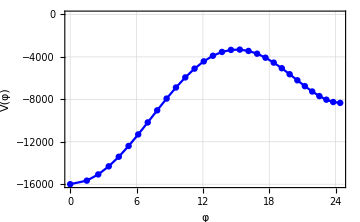

```mathematica
Potential1D = ListPlot[Transpose@{PB2["PathLongitudinal"],PB2["Potential"]},
	Joined->True,
	Mesh->All,
	PlotStyle->Blue,
	Frame->True,
	FrameLabel->{"φ","V(φ)"},
	LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],
	GridLines->Automatic,
	GridLinesStyle->GrayLevel[.85],	
	ImageSize->Medium,	
	PlotRange->All,
	Axes->False]
```